```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"mathutils.m";
```

### (a) Joint Space:

### (b) Choosing points in the Joint Space:

```mathematica
l1Value = 6;
l2Value = 4;
```

```mathematica
randomInputs[l1_,l2_] := {{RandomReal[{0,2*π}],RandomReal[{0,l2}]},{RandomReal[{0,2*π}],RandomReal[{0,l2}]}};
currRandomInputs = randomInputs[l1Value,l2Value];
Print["The 2 chosen random inputs for {θ, d} are ",MatrixForm[currRandomInputs[[1]]]," and ",MatrixForm[currRandomInputs[[2]]]];
```

The 2 chosen random inputs for {θ, d} are (5.72561
2.64097) and (3.82806
2.58934)

### (c) Shortest Path in Joint Space:

```mathematica
shortestPathEq[{θf_,Pf_},{θi_,Pi_},θ_]:=Module[{},
If[!AllTrue[{Pf,θf,Pi,θi},realQ],Return[Print["Error: Please ensure that the joint-space coordinates do not have non-real values"]]];
If[Abs[(θf-θi)]≤π,Return[((Pf-Pi)/(θf-θi))*(θ-θi)+Pi],Return[[Piecewise[{{((Pf-Pi)/(θf-θi-2*π))*(θ-θi)+Pi,θ<θi},{((Pf-Pi)/(θf-θi-2*π))*(θ-θi-2*π)+Pi,θ>θf}}]]]];
];
```

```mathematica
plot1 = ParametricPlot3D[{Cos[θ],Sin[θ],z},{θ,0,2*Pi},{z,0,l2Value},PlotStyle->{Blue,Opacity[0.4]},Mesh-> None];
plot2 = ParametricPlot3D[{Cos[θ],Sin[θ],shortestPathEq[currRandomInputs[[1]],currRandomInputs[[2]],θ]},{θ,Min[{currRandomInputs[[1]][[1]],currRandomInputs[[1]][[2]]}],Max[{currRandomInputs[[1]][[1]],currRandomInputs[[1]][[2]]}]},PlotStyle->Red];
Show[plot1,plot2]
```

-Graphics3D-

### The red line is the geodesic in the joint space.

### (d) Finding corresponding path in Task Space:

```mathematica
fwdKinRP[{l1_,l2_},{θ_,d_}] := Module[{},
Return[{(l1 + d)*Cos[θ],(l1 + d)*Sin[θ]}];
];
```

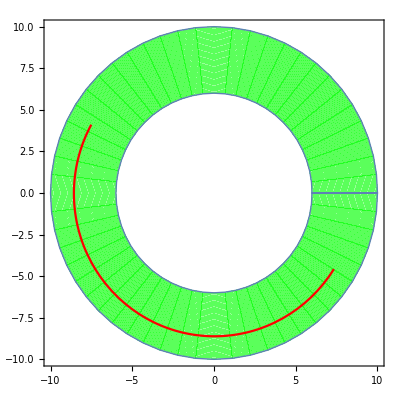

```mathematica
plot4 = ParametricPlot[fwdKinRP[{l1Value,l2Value},{θ,d}],{θ,0,2 π},{d,0,l2Value},PlotStyle->{Green,Opacity[0.4]}];
currSol = fwdKinRP[{l1Value,l2Value},currRandomInputs[[1]]];
geoDesicTaskSpace[θ_] := fwdKinRP[{l1Value,l2Value},{θ,shortestPathEq[currRandomInputs[[1]],currRandomInputs[[2]],θ]}];
plot5 = ParametricPlot[geoDesicTaskSpace[θ], {θ,Min[{currRandomInputs[[1]][[1]],currRandomInputs[[1]][[2]]}],Max[{currRandomInputs[[1]][[1]],currRandomInputs[[1]][[2]]}]},PlotStyle->Red];
Show[plot4,plot5]
```

### The red line is the geodesic in the task space.